```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,500000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[2.7,0.0001,2.7,0,25]
```

$Aborted

```mathematica
Table[tr[1,0.0001,2.7,0,x],{x,Range[1,41,2]}]
```

$Aborted

```mathematica
AbsoluteTiming[tr[2.72,0.0001,2.7,0,21]]
```

{0.05349,10.}

```mathematica
Table[{ω,tr[ω,0.0001,2.7,0,21]},{ω,Range[0,8.5,0.01]}]
```

{{0.,2.85322×10^-7},{0.01,2.8621×10^-7},{0.02,2.88903×10^-7},{0.03,2.93503×10^-7},{0.04,3.00185×10^-7},{0.05,3.09215×10^-7},{0.06,3.20978×10^-7},{0.07,3.36015×10^-7},{0.08,3.55088×10^-7},{0.09,3.79274×10^-7},{0.1,4.10126×10^-7},{0.11,4.49931×10^-7},{0.12,5.02167×10^-7},{0.13,5.7232×10^-7},{0.14,6.69461×10^-7},{0.15,8.09497×10^-7},{0.16,1.02249×10^-6},{0.17,1.37117×10^-6},{0.18,2.00558×10^-6},{0.19,3.3652×10^-6},{0.2,7.25616×10^-6},{0.21,0.0000291107},{0.22,0.991646},{0.23,0.999979},{0.24,0.999995},{0.25,0.999998},{0.26,0.999999},{0.27,0.999999},{0.28,1.},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.},{0.41,1.},{0.42,1.},{0.43,1.},{0.44,1.00001},{0.45,1.00006},{0.46,1.99976},{0.47,1.99999},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.00001},{0.83,2.00006},{0.84,2.99982},{0.85,2.99999},{0.86,2.99999},{0.87,3.},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.00001},{1.17,3.00003},{1.18,3.99865},{1.19,3.99998},{1.2,3.99999},{1.21,4.},{1.22,4.},{1.23,4.},{1.24,4.},{1.25,4.},{1.26,4.},{1.27,4.},{1.28,4.},{1.29,4.},{1.3,4.},{1.31,4.},{1.32,4.},{1.33,4.},{1.34,4.},{1.35,4.},{1.36,4.00001},{1.37,4.00002},{1.38,4.00226},{1.39,4.99997},{1.4,4.99999},{1.41,5.},{1.42,5.},{1.43,5.},{1.44,5.},{1.45,5.},{1.46,5.},{1.47,5.},{1.48,5.},{1.49,5.},{1.5,5.},{1.51,5.},{1.52,5.},{1.53,5.},{1.54,5.},{1.55,5.},{1.56,5.},{1.57,5.},{1.58,5.},{1.59,5.},{1.6,5.},{1.61,5.},{1.62,5.},{1.63,5.},{1.64,5.},{1.65,5.},{1.66,5.},{1.67,5.},{1.68,5.},{1.69,5.},{1.7,5.},{1.71,5.},{1.72,5.},{1.73,5.},{1.74,5.},{1.75,5.},{1.76,5.},{1.77,5.},{1.78,5.},{1.79,5.},{1.8,5.},{1.81,5.},{1.82,5.},{1.83,5.00001},{1.84,5.00032},{1.85,5.99995},{1.86,5.99999},{1.87,6.},{1.88,6.},{1.89,6.},{1.9,6.},{1.91,6.},{1.92,6.00002},{1.93,6.00111},{1.94,6.99997},{1.95,6.99999},{1.96,7.},{1.97,7.},{1.98,7.},{1.99,7.},{2.,7.},{2.01,7.},{2.02,7.},{2.03,7.},{2.04,7.},{2.05,7.},{2.06,7.},{2.07,7.},{2.08,7.},{2.09,7.},{2.1,7.},{2.11,7.},{2.12,7.},{2.13,7.},{2.14,7.},{2.15,7.},{2.16,7.},{2.17,7.},{2.18,7.},{2.19,7.},{2.2,7.00002},{2.21,7.00061},{2.22,7.99996},{2.23,7.99999},{2.24,8.},{2.25,8.},{2.26,8.},{2.27,8.},{2.28,8.},{2.29,8.},{2.3,8.},{2.31,8.},{2.32,8.},{2.33,8.},{2.34,8.},{2.35,8.},{2.36,8.},{2.37,8.},{2.38,8.},{2.39,8.},{2.4,8.},{2.41,8.},{2.42,8.},{2.43,8.},{2.44,8.},{2.45,8.},{2.46,8.},{2.47,8.00002},{2.48,8.00156},{2.49,8.99997},{2.5,8.99999},{2.51,9.},{2.52,9.},{2.53,9.},{2.54,9.},{2.55,9.},{2.56,9.},{2.57,9.},{2.58,9.},{2.59,9.},{2.6,9.},{2.61,9.},{2.62,9.},{2.63,9.00001},{2.64,9.0001},{2.65,9.9999},{2.66,9.99999},{2.67,9.99999},{2.68,10.},{2.69,10.},{2.7,10.},{2.71,10.},{2.72,10.},{2.73,10.},{2.74,10.},{2.75,10.},{2.76,10.},{2.77,10.},{2.78,10.},{2.79,10.},{2.8,10.},{2.81,10.},{2.82,10.},{2.83,10.},{2.84,10.},{2.85,10.},{2.86,10.},{2.87,10.},{2.88,10.},{2.89,10.},{2.9,10.},{2.91,10.},{2.92,10.},{2.93,10.},{2.94,10.},{2.95,10.},{2.96,10.},{2.97,10.},{2.98,10.},{2.99,10.},{3.,10.},{3.01,10.},{3.02,10.},{3.03,10.},{3.04,10.},{3.05,10.},{3.06,10.},{3.07,10.},{3.08,10.},{3.09,10.},{3.1,10.},{3.11,10.},{3.12,10.},{3.13,10.},{3.14,10.},{3.15,10.},{3.16,10.},{3.17,10.},{3.18,10.},{3.19,10.},{3.2,10.},{3.21,10.},{3.22,10.},{3.23,10.},{3.24,10.},{3.25,10.},{3.26,10.},{3.27,10.},{3.28,10.},{3.29,10.},{3.3,10.},{3.31,10.},{3.32,10.},{3.33,10.},{3.34,10.},{3.35,10.},{3.36,10.},{3.37,10.},{3.38,10.},{3.39,10.},{3.4,10.},{3.41,10.},{3.42,10.},{3.43,10.},{3.44,10.},{3.45,9.99999},{3.46,9.99996},{3.47,9.00111},{3.48,9.00002},{3.49,9.},{3.5,9.},{3.51,9.},{3.52,9.},{3.53,9.},{3.54,9.},{3.55,9.},{3.56,9.},{3.57,9.},{3.58,9.},{3.59,9.},{3.6,9.},{3.61,9.},{3.62,9.},{3.63,9.},{3.64,9.},{3.65,9.},{3.66,9.},{3.67,9.},{3.68,9.},{3.69,9.},{3.7,9.},{3.71,9.},{3.72,9.},{3.73,9.},{3.74,9.},{3.75,9.},{3.76,9.},{3.77,9.},{3.78,9.},{3.79,9.},{3.8,9.},{3.81,9.},{3.82,9.},{3.83,9.},{3.84,9.},{3.85,9.},{3.86,9.},{3.87,9.},{3.88,9.},{3.89,9.},{3.9,9.},{3.91,9.},{3.92,9.},{3.93,9.},{3.94,9.},{3.95,9.},{3.96,9.},{3.97,9.},{3.98,9.},{3.99,9.},{4.,9.},{4.01,9.},{4.02,9.},{4.03,9.},{4.04,9.},{4.05,9.},{4.06,9.},{4.07,9.},{4.08,9.},{4.09,9.},{4.1,9.},{4.11,9.},{4.12,9.},{4.13,9.},{4.14,9.},{4.15,9.},{4.16,9.},{4.17,9.},{4.18,9.},{4.19,8.99999},{4.2,8.99999},{4.21,8.99998},{4.22,8.99864},{4.23,8.00003},{4.24,8.},{4.25,8.},{4.26,8.},{4.27,8.},{4.28,8.},{4.29,8.},{4.3,8.},{4.31,8.},{4.32,8.},{4.33,8.},{4.34,8.},{4.35,8.},{4.36,8.},{4.37,8.},{4.38,8.},{4.39,8.},{4.4,8.},{4.41,8.},{4.42,8.},{4.43,8.},{4.44,8.},{4.45,8.},{4.46,8.},{4.47,8.},{4.48,8.},{4.49,8.},{4.5,8.},{4.51,8.},{4.52,8.},{4.53,8.},{4.54,8.},{4.55,8.},{4.56,8.},{4.57,8.},{4.58,8.},{4.59,8.},{4.6,8.},{4.61,8.},{4.62,8.},{4.63,8.},{4.64,8.},{4.65,8.},{4.66,8.},{4.67,8.},{4.68,8.},{4.69,8.},{4.7,8.},{4.71,8.},{4.72,8.},{4.73,8.},{4.74,8.},{4.75,8.},{4.76,8.},{4.77,8.},{4.78,8.},{4.79,8.},{4.8,8.},{4.81,8.},{4.82,8.},{4.83,8.},{4.84,8.},{4.85,8.},{4.86,8.},{4.87,8.},{4.88,8.},{4.89,8.},{4.9,8.},{4.91,8.},{4.92,8.},{4.93,7.99998},{4.94,7.99976},{4.95,7.00005},{4.96,7.00001},{4.97,7.},{4.98,7.},{4.99,7.},{5.,7.},{5.01,7.},{5.02,7.},{5.03,7.},{5.04,7.},{5.05,7.},{5.06,7.},{5.07,7.},{5.08,7.},{5.09,7.},{5.1,7.},{5.11,7.},{5.12,7.},{5.13,7.},{5.14,7.},{5.15,7.},{5.16,7.},{5.17,7.},{5.18,7.},{5.19,7.},{5.2,7.},{5.21,7.},{5.22,7.},{5.23,7.},{5.24,7.},{5.25,7.},{5.26,7.},{5.27,7.},{5.28,7.},{5.29,7.},{5.3,7.},{5.31,7.},{5.32,7.},{5.33,7.},{5.34,7.},{5.35,7.},{5.36,7.},{5.37,7.},{5.38,7.},{5.39,7.},{5.4,7.},{5.41,7.},{5.42,7.},{5.43,7.},{5.44,7.},{5.45,7.},{5.46,7.},{5.47,7.},{5.48,7.},{5.49,7.},{5.5,7.},{5.51,7.},{5.52,7.},{5.53,7.},{5.54,7.},{5.55,7.},{5.56,7.},{5.57,7.},{5.58,7.},{5.59,7.},{5.6,6.99999},{5.61,6.99997},{5.62,6.00837},{5.63,6.00002},{5.64,6.00001},{5.65,6.},{5.66,6.},{5.67,6.},{5.68,6.},{5.69,6.},{5.7,6.},{5.71,6.},{5.72,6.},{5.73,6.},{5.74,6.},{5.75,6.},{5.76,6.},{5.77,6.},{5.78,6.},{5.79,6.},{5.8,6.},{5.81,6.},{5.82,6.},{5.83,6.},{5.84,6.},{5.85,6.},{5.86,6.},{5.87,6.},{5.88,6.},{5.89,6.},{5.9,6.},{5.91,6.},{5.92,6.},{5.93,6.},{5.94,6.},{5.95,6.},{5.96,6.},{5.97,6.},{5.98,6.},{5.99,6.},{6.,6.},{6.01,6.},{6.02,6.},{6.03,6.},{6.04,6.},{6.05,6.},{6.06,6.},{6.07,6.},{6.08,6.},{6.09,6.},{6.1,6.},{6.11,6.},{6.12,6.},{6.13,6.},{6.14,6.},{6.15,6.},{6.16,6.},{6.17,6.},{6.18,6.},{6.19,6.},{6.2,6.},{6.21,6.},{6.22,5.99999},{6.23,5.99994},{6.24,5.00018},{6.25,5.00001},{6.26,5.},{6.27,5.},{6.28,5.},{6.29,5.},{6.3,5.},{6.31,5.},{6.32,5.},{6.33,5.},{6.34,5.},{6.35,5.},{6.36,5.},{6.37,5.},{6.38,5.},{6.39,5.},{6.4,5.},{6.41,5.},{6.42,5.},{6.43,5.},{6.44,5.},{6.45,5.},{6.46,5.},{6.47,5.},{6.48,5.},{6.49,5.},{6.5,5.},{6.51,5.},{6.52,5.},{6.53,5.},{6.54,5.},{6.55,5.},{6.56,5.},{6.57,5.},{6.58,5.},{6.59,5.},{6.6,5.},{6.61,5.},{6.62,5.},{6.63,5.},{6.64,5.},{6.65,5.},{6.66,5.},{6.67,5.},{6.68,5.},{6.69,5.},{6.7,5.},{6.71,5.},{6.72,5.},{6.73,5.},{6.74,5.},{6.75,5.},{6.76,4.99999},{6.77,4.99998},{6.78,4.99774},{6.79,4.00003},{6.8,4.00001},{6.81,4.},{6.82,4.},{6.83,4.},{6.84,4.},{6.85,4.},{6.86,4.},{6.87,4.},{6.88,4.},{6.89,4.},{6.9,4.},{6.91,4.},{6.92,4.},{6.93,4.},{6.94,4.},{6.95,4.},{6.96,4.},{6.97,4.},{6.98,4.},{6.99,4.},{7.,4.},{7.01,4.},{7.02,4.},{7.03,4.},{7.04,4.},{7.05,4.},{7.06,4.},{7.07,4.},{7.08,4.},{7.09,4.},{7.1,4.},{7.11,4.},{7.12,4.},{7.13,4.},{7.14,4.},{7.15,4.},{7.16,4.},{7.17,4.},{7.18,4.},{7.19,4.},{7.2,4.},{7.21,4.},{7.22,4.},{7.23,3.99998},{7.24,3.99967},{7.25,3.00005},{7.26,3.00001},{7.27,3.},{7.28,3.},{7.29,3.},{7.3,3.},{7.31,3.},{7.32,3.},{7.33,3.},{7.34,3.},{7.35,3.},{7.36,3.},{7.37,3.},{7.38,3.},{7.39,3.},{7.4,3.},{7.41,3.},{7.42,3.},{7.43,3.},{7.44,3.},{7.45,3.},{7.46,3.},{7.47,3.},{7.48,3.},{7.49,3.},{7.5,3.},{7.51,3.},{7.52,3.},{7.53,3.},{7.54,3.},{7.55,3.},{7.56,3.},{7.57,3.},{7.58,3.},{7.59,2.99999},{7.6,2.99998},{7.61,2.99938},{7.62,2.00004},{7.63,2.00001},{7.64,2.},{7.65,2.},{7.66,2.},{7.67,2.},{7.68,2.},{7.69,2.},{7.7,2.},{7.71,2.},{7.72,2.},{7.73,2.},{7.74,2.},{7.75,2.},{7.76,2.},{7.77,2.},{7.78,2.},{7.79,2.},{7.8,2.},{7.81,2.},{7.82,2.},{7.83,2.},{7.84,2.},{7.85,2.},{7.86,1.99999},{7.87,1.99998},{7.88,1.99844},{7.89,1.00003},{7.9,1.00001},{7.91,1.},{7.92,1.},{7.93,1.},{7.94,1.},{7.95,1.},{7.96,1.},{7.97,1.},{7.98,1.},{7.99,0.999999},{8.,0.999999},{8.01,0.999998},{8.02,0.999996},{8.03,0.999989},{8.04,0.999901},{8.05,0.000101362},{8.06,0.0000112032},{8.07,4.06283×10^-6},{8.08,2.09794×10^-6},{8.09,1.2881×10^-6},{8.1,8.76725×10^-7},{8.11,6.38922×10^-7},{8.12,4.88763×10^-7},{8.13,3.87651×10^-7},{8.14,3.16152×10^-7},{8.15,2.63609×10^-7},{8.16,2.23778×10^-7},{8.17,1.92801×10^-7},{8.18,1.6819×10^-7},{8.19,1.48277×10^-7},{8.2,1.31912×10^-7},{8.21,1.18279×10^-7},{8.22,1.06788×10^-7},{8.23,9.69995×10^-8},{8.24,8.8584×10^-8},{8.25,8.12887×10^-8},{8.26,7.49172×10^-8},{8.27,6.93151×10^-8},{8.28,6.43592×10^-8},{8.29,5.99506×10^-8},{8.3,5.6009×10^-8},{8.31,5.24683×10^-8},{8.32,4.92743×10^-8},{8.33,4.63814×10^-8},{8.34,4.37517×10^-8},{8.35,4.13531×10^-8},{8.36,3.91582×10^-8},{8.37,3.7144×10^-8},{8.38,3.52903×10^-8},{8.39,3.358×10^-8},{8.4,3.1998×10^-8},{8.41,3.05315×10^-8},{8.42,2.91691×10^-8},{8.43,2.79008×10^-8},{8.44,2.67178×10^-8},{8.45,2.56123×10^-8},{8.46,2.45776×10^-8},{8.47,2.36075×10^-8},{8.48,2.26965×10^-8},{8.49,2.18397×10^-8},{8.5,2.10328×10^-8}}

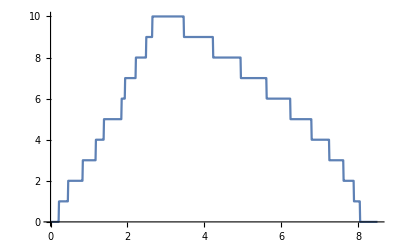

```mathematica
ListPlot[%33,Joined->True]
```